```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
totalData=Import["helical_coil_data.txt","Table"];
(* delete column with currents *)
coilData=Drop[totalData,None,{4}];
phiAngle=ArcTan[coilData[[;;,1]],coilData[[;;,2]]];
phiAngle=Mod[phiAngle,2Pi];
```

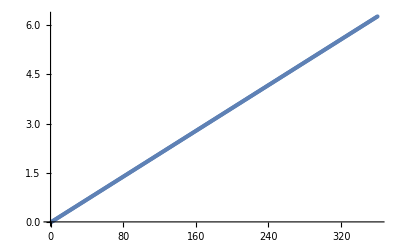

```mathematica
ListPlot[phiAngle]
```

```mathematica
(* Model of helical coil*)
```

```mathematica
(* Helical Coils *)
```

```mathematica
Rc=4.;
Zc=0.;
ac=0.9;
pitch=0.1;
m=5;

RCoil1=Rc+ac*Cos[m*ϕ+pitch*Sin[m*ϕ]];
ZCoil1=Zc+ac*Sin[m*ϕ+pitch*Sin[m*ϕ]];
xCoil1=RCoil1*Cos[ϕ];
yCoil1=RCoil1*Sin[ϕ];
zCoil1=ZCoil1;
xyzCoil1={xCoil1,yCoil1,zCoil1};
```

```mathematica
Show[ListPointPlot3D[coilData],ParametricPlot3D[xyzCoil1,{ϕ,0.,2.Pi},PlotStyle->Orange],AxesLabel->{x,y,z},ViewPoint->Top]
```

-Graphics3D-